```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

If you use FeynArts in your research, please cite

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../FA_models/SMS-stop-FA/SMS-stop-FA_CT",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs}];
```

## g-g- t- t (effective vertex)

The choice below for the momenta and the ordering of the particles in the process is equivalent to the correct
ordering for computing the effective vertex for the UFO format:
0 →4, with {} →{-F[9],F[9],V[4],V[4]} and all the momenta set as outgoing ({} → {p1,p2,p3,p4}).
However the choice below produces nicer diagrams.

```mathematica
tops = CreateTopologies[0,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,WFCorrections}];
processGGT = { V[4],V[4]} -> {F[9],-F[9]};
allDiags = InsertFields[tops,processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[3],V[1],V[4],S[1],S[2],S[3],V[2],F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8]}];
goodDiags=DiagramExtract[allDiags,{1}];
topsL = CreateTopologies[1,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,WFCorrections}];
allDiagsL = InsertFields[topsL,processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[3],V[1],S[1],S[2],S[3],V[2],F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8]}];
goodDiagsL=DiagramExtract[allDiagsL,{54}];
```

in total: 2 Particles insertions

in total: 57 Particles insertions

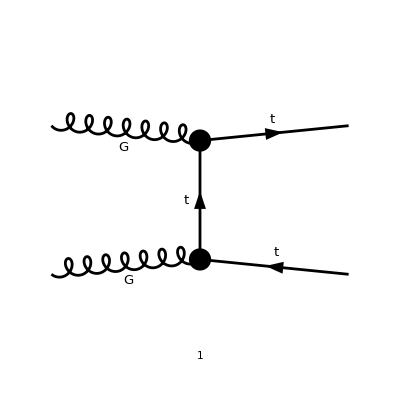

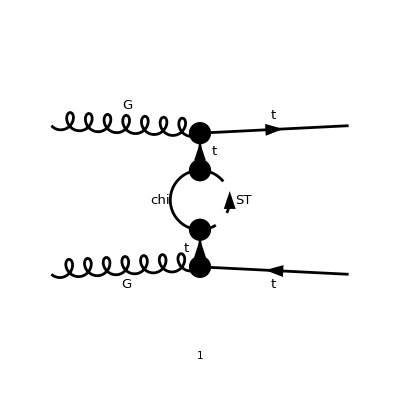

```mathematica
Paint[goodDiags,ColumnsXRows->{1,1},ImageSize->{ 150,150},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
Paint[goodDiagsL,ColumnsXRows->{1,1},ImageSize->{ 150,150},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
|
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{pa,pb},LorentzIndexNames->{a,b},OutgoingMomenta->{k1,k2},SUNIndexNames->{cc3,cc4,aa,bb},SUNFIndexNames->{c1,c2},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs,deltaCTL->0,deltaCTR->0}
```

in total: 1 Particles amplitude

-(ⅈ (ⅈ gs γ^a.(γ̄)^6 T_Col3Col5^cc3+ⅈ gs γ^a.(γ̄)^7 T_Col3Col5^cc3).(MT-γ·(k2-pb)).(ⅈ gs γ^b.(γ̄)^6 T_Col5Col4^cc4+ⅈ gs γ^b.(γ̄)^7 T_Col5Col4^cc4))/((k2-pb)^2-MT^2)

```mathematica
ampAL=FCFAConvert[CreateFeynAmp[goodDiagsL,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{pa,pb},LorentzIndexNames->{a,b},OutgoingMomenta->{k1,k2},SUNIndexNames->{cc3,cc4,aa,bb},SUNFIndexNames->{c1,c2},LoopMomenta->{-q},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs,deltaCTL->0,deltaCTR->0}
```

in total: 1 Particles amplitude

-((ⅈ gs γ^a.(γ̄)^6 T_Col3Col5^cc3+ⅈ gs γ^a.(γ̄)^7 T_Col3Col5^cc3).(MT-γ·(k2-pb)).(-ⅈ yDM (γ̄)^7).(mChi+γ·q).(-ⅈ yDM (γ̄)^6).(MT-γ·(k2-pb)).(ⅈ gs γ^b.(γ̄)^6 T_Col5Col4^cc4+ⅈ gs γ^b.(γ̄)^7 T_Col5Col4^cc4))/(((k2-pb)^2-MT^2)^2 (q^2-mChi^2).((k2-pb+q)^2-mST^2))

```mathematica
ampB=Simplify[ampA]/.{DiracGamma[LorentzIndex[a,D],D].DiracGamma[6]+DiracGamma[LorentzIndex[a,D],D].DiracGamma[7]->DiracGamma[LorentzIndex[a,D],D],DiracGamma[LorentzIndex[b,D],D].DiracGamma[6]+DiracGamma[LorentzIndex[b,D],D].DiracGamma[7]->DiracGamma[LorentzIndex[b,D],D] };
ampBL=Simplify[ampAL]/.{DiracGamma[LorentzIndex[a,D],D].DiracGamma[6]+DiracGamma[LorentzIndex[a,D],D].DiracGamma[7]->DiracGamma[LorentzIndex[a,D],D],DiracGamma[LorentzIndex[b,D],D].DiracGamma[6]+DiracGamma[LorentzIndex[b,D],D].DiracGamma[7]->DiracGamma[LorentzIndex[b,D],D] };
```

```mathematica
effVertex[pt_,ptb_,a_]:=I Pi^2 yDM^2FeynAmpDenominator[PropagatorDenominator[Momentum[pt,D],MT]]* b1[pt^2,mChi^2,mST^2]DiracGamma[LorentzIndex[ a,D],D].(MT DiracGamma[Momentum[pt,D],D]+ Pair[Momentum[pt,D],Momentum[pt,D]] ).DiracGamma[6]+I Pi^2 yDM^2FeynAmpDenominator[PropagatorDenominator[Momentum[ptb,D],MT]]* b1[ptb^2,mChi^2,mST^2] DiracGamma[7].(-MT DiracGamma[Momentum[ptb,D],D]+ Pair[Momentum[ptb,D],Momentum[ptb,D]] ).DiracGamma[LorentzIndex[ a,D],D];
```

```mathematica
ampB1=FullSimplify[ampB/.{gs*DiracGamma[LorentzIndex[a,D],D]->gs effVertex[k1,pb-k2,a]}]
```

-(ⅈ (π^2 (-gs) yDM^2 T_Col3Col5^cc3 ((b1((k2-pb)^2,mChi^2,mST^2) (γ̄)^7.((pb-k2)^2-MT γ·(pb-k2)).γ^a)/((pb-k2)^2-MT^2)+(b1(k1^2,mChi^2,mST^2) γ^a.(MT γ·k1+k1^2).(γ̄)^6)/(k1^2-MT^2))).(MT-γ·(k2-pb)).(ⅈ gs γ^b T_Col5Col4^cc4))/((k2-pb)^2-MT^2)

```mathematica
ampB2=FullSimplify[ampB/.{gs*DiracGamma[LorentzIndex[b,D],D]->gs effVertex[pb-k2,k2,b]}]
```

-(ⅈ (ⅈ gs γ^a T_Col3Col5^cc3).(MT-γ·(k2-pb)).(π^2 (-gs) yDM^2 T_Col5Col4^cc4 ((b1((k2-pb)^2,mChi^2,mST^2) γ^b.((pb-k2)^2+MT γ·(pb-k2)).(γ̄)^6)/((pb-k2)^2-MT^2)+(b1(k2^2,mChi^2,mST^2) (γ̄)^7.(k2^2-MT γ·k2).γ^b)/(k2^2-MT^2))))/((k2-pb)^2-MT^2)

```mathematica
ampC=FullSimplify[ampB1+ampB2]
```

-1/((k2-pb)^2-MT^2)ⅈ ((π^2 (-gs) yDM^2 T_Col3Col5^cc3 ((b1((k2-pb)^2,mChi^2,mST^2) (γ̄)^7.((pb-k2)^2-MT γ·(pb-k2)).γ^a)/((pb-k2)^2-MT^2)+(b1(k1^2,mChi^2,mST^2) γ^a.(MT γ·k1+k1^2).(γ̄)^6)/(k1^2-MT^2))).(MT-γ·(k2-pb)).(ⅈ gs γ^b T_Col5Col4^cc4)+(ⅈ gs γ^a T_Col3Col5^cc3).(MT-γ·(k2-pb)).(π^2 (-gs) yDM^2 T_Col5Col4^cc4 ((b1((k2-pb)^2,mChi^2,mST^2) γ^b.((pb-k2)^2+MT γ·(pb-k2)).(γ̄)^6)/((pb-k2)^2-MT^2)+(b1(k2^2,mChi^2,mST^2) (γ̄)^7.(k2^2-MT γ·k2).γ^b)/(k2^2-MT^2))))

```mathematica
b21rep={((-I)*yDM*DiracGamma[7]).(mChi+DiracGamma[Momentum[q,D],D]).((-I)*yDM*DiracGamma[6])-> I Pi^2 yDM^2 DiracGamma[Momentum[pb-k2,D],D].DiracGamma[6] b1[(k2-pb)^2,mChi^2,mST^2],FeynAmpDenominator[PropagatorDenominator[-Momentum[q,D],mChi],PropagatorDenominator[-Momentum[k2-pb+q,D],mST]]->1}
```

{(-ⅈ yDM (γ̄)^7).(mChi+γ·q).(-ⅈ yDM (γ̄)^6)→ⅈ π^2 yDM^2 (γ·(pb-k2)).(γ̄)^6 b1((k2-pb)^2,mChi^2,mST^2),1/((q^2-mChi^2).((k2-pb+q)^2-mST^2))→1}

```mathematica
ampCL=FullSimplify[ampBL/.b21rep]
```

-((ⅈ gs γ^a T_Col3Col5^cc3).(MT-γ·(k2-pb)).(ⅈ π^2 yDM^2 (γ·(pb-k2)).(γ̄)^6 b1((k2-pb)^2,mChi^2,mST^2)).(MT-γ·(k2-pb)).(ⅈ gs γ^b T_Col5Col4^cc4))/(((k2-pb)^2-MT^2)^2)

```mathematica
FullSimplify[DiracSimplify[FullSimplify[FeynAmpDenominatorExplicit[ampCL]],DiracOrder->True]]
```

1/((-2 (k2·pb)+k2^2-MT^2+pb^2)^2)ⅈ π^2 gs^2 yDM^2 T_Col3Col5^cc3 T_Col5Col4^cc4 b1((k2-pb)^2,mChi^2,mST^2) (-2 k2^2 k2^b γ^a.(γ̄)^6+k2^2 γ^a.γ^b.(γ·k2).(γ̄)^6-2 MT^2 k2^b γ^a.(γ̄)^7+MT^2 γ^a.γ^b.(γ·k2).(γ̄)^7+k2^2 MT γ^a.γ^b.(γ̄)^6+k2^2 MT γ^a.γ^b.(γ̄)^7-2 MT (k2·pb) γ^a.γ^b.(γ̄)^6-2 MT (k2·pb) γ^a.γ^b.(γ̄)^7+pb^2 (γ^a.γ^b.(γ·k2).(γ̄)^6+2 γ^a.(γ̄)^6 (pb^b-k2^b)+MT (γ^a.γ^b.(γ̄)^6+γ^a.γ^b.(γ̄)^7)-γ^a.γ^b.(γ·pb).(γ̄)^6)+2 k2^2 pb^b γ^a.(γ̄)^6+4 k2^b γ^a.(γ̄)^6 (k2·pb)-4 pb^b γ^a.(γ̄)^6 (k2·pb)-2 (k2·pb) γ^a.γ^b.(γ·k2).(γ̄)^6+2 (k2·pb) γ^a.γ^b.(γ·pb).(γ̄)^6-k2^2 γ^a.γ^b.(γ·pb).(γ̄)^6+2 MT^2 pb^b γ^a.(γ̄)^7-MT^2 γ^a.γ^b.(γ·pb).(γ̄)^7)

```mathematica
FullSimplify[DiracSimplify[FullSimplify[FeynAmpDenominatorExplicit[ampC/.{b1[k1^2,a_,b_]-> 0,b1[k2^2,a_,b_]-> 0}]],DiracOrder->True]]
```

-1/((-2 (k2·pb)+k2^2-MT^2+pb^2)^2)2 π^2 gs^2 yDM^2 T_Col3Col5^cc3 T_Col5Col4^cc4 b1((k2-pb)^2,mChi^2,mST^2) (-2 k2^2 k2^b γ^a.(γ̄)^6+k2^2 γ^a.γ^b.(γ·k2).(γ̄)^6-MT^2 k2^b γ^a.(γ̄)^6+MT^2 γ^b.(γ̄)^6 (k2^a-pb^a)-2 MT (γ̄)^7 k2^a k2^b+k2^2 MT γ^a.γ^b.(γ̄)^7+MT k2^b γ^a.(γ·k2).(γ̄)^6+2 MT (γ̄)^7 pb^a k2^b+2 MT (γ̄)^7 k2^a pb^b-2 MT (k2·pb) γ^a.γ^b.(γ̄)^7-MT k2^a γ^b.(γ·pb).(γ̄)^7+MT (k2^a-pb^a) γ^b.(γ·k2).(γ̄)^7-MT k2^b γ^a.(γ·pb).(γ̄)^6-MT pb^b γ^a.(γ·k2).(γ̄)^6+pb^2 (γ^a.γ^b.(γ·k2).(γ̄)^6+2 γ^a.(γ̄)^6 (pb^b-k2^b)+MT γ^a.γ^b.(γ̄)^7-γ^a.γ^b.(γ·pb).(γ̄)^6)+2 k2^2 pb^b γ^a.(γ̄)^6+4 k2^b γ^a.(γ̄)^6 (k2·pb)-4 pb^b γ^a.(γ̄)^6 (k2·pb)-2 (k2·pb) γ^a.γ^b.(γ·k2).(γ̄)^6+2 (k2·pb) γ^a.γ^b.(γ·pb).(γ̄)^6-k2^2 γ^a.γ^b.(γ·pb).(γ̄)^6+MT^2 pb^b γ^a.(γ̄)^6-2 MT (γ̄)^7 pb^a pb^b+MT pb^a γ^b.(γ·pb).(γ̄)^7+MT pb^b γ^a.(γ·pb).(γ̄)^6)

## Check Divergences

```mathematica
lInts = Cases2[ampC,{A0,B0,C0,D0,PaVe}];
Table[{lInts[[i]],PaXEvaluateUV[lInts[[i]],PaXImplicitPrefactor->1/(2 Pi)^(4)]},{i,1,Length[lInts]}]
```

(A_0(mChi^2) | mChi^2/(16 π^4 ε_UV)
A_0(mST^2) | mST^2/(16 π^4 ε_UV)
B_0(k1^2,mChi^2,mST^2) | 1/(16 π^4 ε_UV)
B_0(k2^2,mChi^2,mST^2) | 1/(16 π^4 ε_UV)
B_0((k2-pb)^2,mChi^2,mST^2) | 1/(16 π^4 ε_UV))

```mathematica
lIntsL = Cases2[ampCL,{A0,B0,C0,D0,PaVe}];
Table[{lIntsL[[i]],PaXEvaluateUV[lIntsL[[i]],PaXImplicitPrefactor->1/(2 Pi)^(4)]},{i,1,Length[lIntsL]}]
```

(A_0(mChi^2) | mChi^2/(16 π^4 ε_UV)
A_0(mST^2) | mST^2/(16 π^4 ε_UV)
B_0(k2^2-2 (k2·pb)+pb^2,mChi^2,mST^2) | 1/(16 π^4 ε_UV)
B_0(k2^2-2 (k2·pb)+pb^2,mChi^2,mST^2) | 1/(16 π^4 ε_UV))

```mathematica
(* Divergences from loops *)
loopUV=FullSimplify[PaXEvaluateUV[ampC,PaXImplicitPrefactor->1/(2 Pi)^(4)]];
DiracSimplify[FullSimplify[FeynAmpDenominatorExplicit[DiracSimplify[(loopUV),DiracSubstitute67->True,DiracOrder->True]]]]
```

## Coefficients for Loop Amplitude

```mathematica
subs2={B0[a_,mChi^2,mST^2]:>(ab[a]+(A0[mST^2]-A0[mChi^2]))/(mST^2-mChi^2-a)};
```

```mathematica
ampEsimp3=FeynAmpDenominatorExplicit[DiracSimplify[ampEsimp2/.subs]]/.subs2;
```

```mathematica
spinorChains1=Tally[Cases[{ampEsimp3},DiracGamma[___],All]][[All,1]];
spinorChains2=Tally[Cases[{ampEsimp3},DiracGamma[___].DiracGamma[___],All]][[All,1]];
spinorChains3=Tally[Cases[{ampEsimp3},DiracGamma[___].DiracGamma[___].DiracGamma[___],All]][[All,1]];
spinorChains4=Tally[Cases[{ampEsimp3},DiracGamma[___].DiracGamma[___].DiracGamma[___].DiracGamma[___],All]][[All,1]];
allTerms=Sort[Join[spinorChains1,spinorChains2,spinorChains3,spinorChains4]]
su3prods=Join[Cases2[ampEsimp3,SUNTF],Cases2[ampEsimp3,SUNF]]
```

### Coefficients for each term

Define shortnames for each coefficient

```mathematica
subs3={(-(MT (-ab[a_] + 2 deltaS MT + 2 deltaSp a_))/(2 (MT^2-a_)^2)):> ab1[s,a],
(2 a_ ( 2 deltaS  MT^2 - deltaS a_ + deltaSp MT^3) - MT^3 ab[a_])/(2 MT a_ (MT^2-a_)^2):> ab2[s,a],
(2 a_ (  deltaS  +deltaSp MT) - MT ab[a_])/(2 MT a_ (MT^2-a_)):> ab3[s,a],
-(-(MT (-ab[a_] + 2 deltaS MT + 2 deltaSp a_))/(2 (MT^2-a_)^2)):> -ab1[s,a],
((MT^3 ab[a_]+2 a_ (deltaS a_ -MT^2( 2 deltaS +  deltaSp MT)))/(2 MT a_ (MT^2-a_)^2)):> -ab2[s,a],
-((2 a_ (  deltaS  +deltaSp MT) - MT ab[a_])/(2 MT a_ (MT^2-a_))):> -ab3[s,a]
};
```

```mathematica
su3Terms={};
Do[c=FullSimplify[Coefficient[Coefficient[Expand[ampEsimp3],su3prods[[i]]],allTerms[[j]]]];
If[c==0,Continue[]];
c= Collect[c/(I Pi^2 gs^2 yDM^2),{MT,t,u},FullSimplify]/.subs3;
AppendTo[su3Terms,{su3prods[[i]],allTerms[[j]],c}];
,{i,1,Length[su3prods]},{j,1,Length[allTerms]}];
```

#### Check that all terms have been correctly split

```mathematica
ampTot = I Pi^2 gs^2 yDM^2 Sum[su3Terms[[i,1]] su3Terms[[i,2]] su3Terms[[i,3]],{i,1,Length[su3Terms]}]; 
Simplify[ampTot-ampEsimp3]
```

```mathematica
su3Terms
```

## Construct ALOHA terms

UFO conventions:
ProjM -> Gamma[7], ProjP -> Gamma[6]
particles = [ P.t__tilde __, P.t, P.g, P.g ] ] = [ p1=P(*,1),  p2=P(*,2), p3(μ)=P(*,3), p4(ν)=P(*,4) ] (all momenta are incoming)
 c1 = Anti-Top color = “1”, c2 = Top color = “2”, c3 = Gluon color = “3”, c4 = Gluon color = “4”
spins = [2, 2, 3], 
structure = ‘ P (4, 3)*Gamma (3, 2, -1)*ProjP (-1, 1) - P (3, 4)*Gamma (4, 2, -1)*ProjP (-1, 1)’)

s = (p1+p2)^2 =  P(-1,1)**2 + P(-1,2)**2 + 2*P(-1,1)*P(-1,2)
t = (p1+p3)^2  = P(-1,1)**2 + P(-1,3)**2 + 2*P(-1,1)*P(-1,3)
u = (p1+p4)^2  = (p2+p3)^2 = P(-1,2)**2 + P(-1,3)**2 + 2*P(-1,2)*P(-1,3) 
(The indices of the product of gamma matrices are always M(2,1), since the second (outgoing) top is contract to the left and the first (incoming) to the right)

```mathematica
su3Matrices=Tally[su3Terms[[All,1]]][[All,1]]
tensors=Tally[su3Terms[[All,2]]][[All,1]]
```

```mathematica
su3Replacements={SUNTF[{SUNIndex[cc3],SUNIndex[cc4]},SUNFIndex[c2],SUNFIndex[c1]]-> "T(3,2,-1)*T(4,-1,1)",
                                   SUNTF[{SUNIndex[cc4],SUNIndex[cc3]},SUNFIndex[c2],SUNFIndex[c1]]->  "T(4,2,-1)*T(3,-1,1)"};
```

```mathematica
tensorReplacements={DiracGamma[LorentzIndex[μ,D],D].DiracGamma[LorentzIndex[ν,D],D]-> "Gamma(3,2,-1)*Gamma(4,-1,1)",
				   DiracGamma[LorentzIndex[ν,D],D].DiracGamma[LorentzIndex[μ,D],D]-> "Gamma(4,2,-1)*Gamma(3,-1,1)",
DiracGamma[LorentzIndex[μ, D], D] . DiracGamma[Momentum[p1, D], D] . DiracGamma[LorentzIndex[ν, D], D]->  "Gamma(3,2,-1)*P(-2,1)*Gamma(-2,-1,-3)*Gamma(4,-3,1)",
DiracGamma[LorentzIndex[ν, D], D] . DiracGamma[Momentum[p1, D], D] . DiracGamma[LorentzIndex[μ, D], D]->  "Gamma(4,2,-1)*P(-2,1)*Gamma(-2,-1,-3)*Gamma(3,-3,1)",DiracGamma[LorentzIndex[μ, D], D] . DiracGamma[Momentum[p2, D], D] . DiracGamma[LorentzIndex[ν, D], D]->  "Gamma(3,2,-1)*P(-2,2)*Gamma(-2,-1,-3)*Gamma(4,-3,1)",DiracGamma[LorentzIndex[ν, D], D] . DiracGamma[Momentum[p2, D], D] . DiracGamma[LorentzIndex[μ, D], D]->  "Gamma(4,2,-1)*P(-2,2)*Gamma(-2,-1,-3)*Gamma(3,-3,1)",
DiracGamma[LorentzIndex[μ, D], D] . DiracGamma[Momentum[p3, D], D] . DiracGamma[LorentzIndex[ν, D], D]->  "Gamma(3,2,-1)*P(-2,3)*Gamma(-2,-1,-3)*Gamma(4,-3,1)",DiracGamma[LorentzIndex[ν, D], D] . DiracGamma[Momentum[p3, D], D] . DiracGamma[LorentzIndex[μ, D], D]->  "Gamma(4,2,-1)*P(-2,3)*Gamma(-2,-1,-3)*Gamma(3,-3,1)",
DiracGamma[LorentzIndex[μ, D], D] . DiracGamma[Momentum[p1, D], D] . DiracGamma[LorentzIndex[ν, D], D]. DiracGamma[6]->  "Gamma(3,2,-1)*P(-2,1)*Gamma(-2,-1,-3)*Gamma(4,-3,-4)*ProjP(-4,1)",
DiracGamma[LorentzIndex[ν, D], D] . DiracGamma[Momentum[p1, D], D] . DiracGamma[LorentzIndex[μ, D], D]. DiracGamma[6]->  "Gamma(4,2,-1)*P(-2,1)*Gamma(-2,-1,-3)*Gamma(3,-3,-4)*ProjP(-4,1)",
DiracGamma[LorentzIndex[μ, D], D] . DiracGamma[Momentum[p3, D], D] . DiracGamma[LorentzIndex[ν, D], D]. DiracGamma[6]->  "Gamma(3,2,-1)*P(-2,3)*Gamma(-2,-1,-3)*Gamma(4,-3,-4)*ProjP(-4,1)",
DiracGamma[LorentzIndex[ν, D], D] . DiracGamma[Momentum[p3, D], D] . DiracGamma[LorentzIndex[μ, D], D]. DiracGamma[6]->  "Gamma(4,2,-1)*P(-2,3)*Gamma(-2,-1,-3)*Gamma(3,-3,-4)*ProjP(-4,1)",
DiracGamma[LorentzIndex[μ, D], D] . DiracGamma[Momentum[p2, D], D] . DiracGamma[LorentzIndex[ν, D], D]. DiracGamma[6]->  "Gamma(3,2,-1)*P(-2,2)*Gamma(-2,-1,-3)*Gamma(4,-3,-4)*ProjP(-4,1)",
DiracGamma[LorentzIndex[ν, D], D] . DiracGamma[Momentum[p2, D], D] . DiracGamma[LorentzIndex[μ, D], D]. DiracGamma[6]->  "Gamma(4,2,-1)*P(-2,2)*Gamma(-2,-1,-3)*Gamma(3,-3,-4)*ProjP(-4,1)"};
```

```mathematica
tensorReplacements = SortBy[tensorReplacements,-StringLength[ToString[#]]&]
```

### Print each Lorentz structure as a distinct Lorentz vertex :

```mathematica
vertexCounter=20;
Do[
Print["------------------"];
Print[su3Matrices[[n]]/.su3Replacements];
(* Select all terms containing the desired SU3 matrix *)
terms0=Select[su3Terms,#[[1]]==su3Matrices[[n]]&];
Do[
(* Select all terms containing the desired gamma structure *)
terms1=Select[terms0,#[[2]]==tensors[[m]]&];
If[Length[terms1]==0,Continue[]];
vertexCounter += 1;
Print[StringJoin["FFVVNP",ToString[vertexCounter]]];
(* Print[tensors[[m]]/.tensorReplacements];*)
(* Compute the ALOHA term for this tensor/gamma structure and color factor *)
terms=StringJoin["(",ToString[FortranForm[terms1[[1,3]]]],")"];
(*terms=Table[StringJoin["     ",terms[[i]]],{i,1,Length[terms]}];*)
fullStr = StringJoin[terms];
fullStr = StringJoin["( ",tensors[[m]]/.tensorReplacements," )*(",fullStr,")"];
 Print[fullStr];
,{m,1,Length[tensors]}]
,{n,1,Length[su3Matrices]}]
```

#### Write to File

```mathematica
fileName="../../Models/Top-FormFactorsOneLoop-UFO/lffvvnpSelf.txt";
outF = OpenWrite[fileName,PageWidth->Infinity];
vertexCounter=20;
Do[
Write[outF,"------------------"];
Write[outF,su3Matrices[[n]]/.su3Replacements];
(* Select all terms containing the desired SU3 matrix *)
terms0=Select[su3Terms,#[[1]]==su3Matrices[[n]]&];
Do[
(* Select all terms containing the desired gamma structure *)
terms1=Select[terms0,#[[2]]==tensors[[m]]&];
If[Length[terms1]==0,Continue[]];
vertexCounter += 1;
Write[outF,StringJoin["FFVVNP",ToString[vertexCounter]]];
(* Compute the ALOHA term for this tensor/gamma structure and color factor *)
terms=StringJoin["(",ToString[FortranForm[terms1[[1,3]]]],")"];
fullStr = StringJoin[terms];
fullStr = StringJoin["( ",tensors[[m]]/.tensorReplacements," )*( ",fullStr,")"];
 Write[outF,fullStr];
,{m,1,Length[tensors]}]
,{n,1,Length[su3Matrices]}]
Close[outF]
```